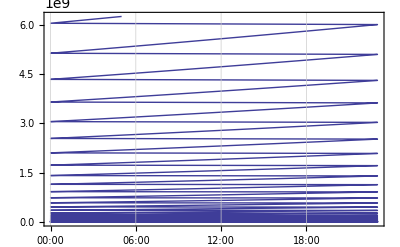

```mathematica
f[x_]=
Fit[
Table[
{i,Data[VC][[4]][[i]]},{i,L}](*Iterate over every time period*)
(*how to find line in data*)
,{1,x,x^2,x^3,x^4,x^5,x^6},x];
pd=Table[{Fdate[i],f[i]},{i,L*10}];
DateListPlot[pd,{FFdate[1],Fdate[L]},Joined->True]


(*data={{0,1},{1,0},{3,2},{5,4}};
Fit[data,{1,x},x]
F=Fit[data,{1,x},x];
f[x_]=F;
pp=Fun[VC][[2]]
ppp[x_]=P
ppp[1]
f[1]*)
```

```mathematica
Table[

Table[
{i,Data[VC][[1]][[i]]},{i,L}](*Iterate over every time period*)
(*how to find line in data*)
,{1,x,x^2,x^3,x^4,x^5,x^6},x],
{n,1}]
(*f[x_]=ff
Table[{Fdate[i],f[i]},{i,L}]
*)
```

Table::itform: Argument f[n][x_] = f ; at position 2 does not have the correct form for an iterator.

Table[f=Fit[Table[{i,Data[VC]⟦1⟧⟦i⟧},{i,L}],{1,x,x^2,x^3,x^4,x^5,x^6},x],f[n][x_]=f;,{n,1}]

```mathematica
Data[VC][[1]][[1]]
```

0

```mathematica
data=Table[x^2,{x,1,10}]

(* ==>{1,4,9,16,25,36,49,64,81,100}*)

f[x_]=Fit[data,{1,x},x]


f[1]
```

{1,4,9,16,25,36,49,64,81,100}

-22.+11. x

-11.